# Modelo versión 3

## Pruebas 30/07

## Importación de la red:

Pasar a SetDirectory el directorio en donde se encuentra el archivo .graphml para facilidad

Tener en cuenta que i debe cumplir con los valores de num-people

```mathematica
SetDirectory[NotebookDirectory[]];
```

Capacity=1

```mathematica
ivals={100,200,300,400,500,600,700,800,900,1000};
jvals={1000,2000,3000,4000,5000,6000,7000,8000,9000,10000};
networksM3=Table[Import[StringJoin["graphs/model-v3/capacity1/","network-",IntegerString[ivals[[i]]],"-",IntegerString[jvals[[i]]],".graphml"]],{i,1,10,1}];
```

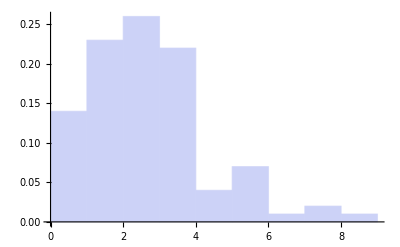
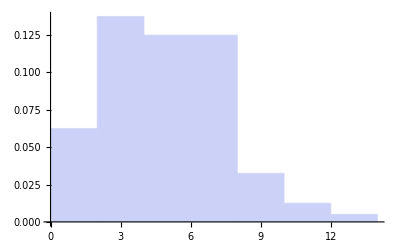
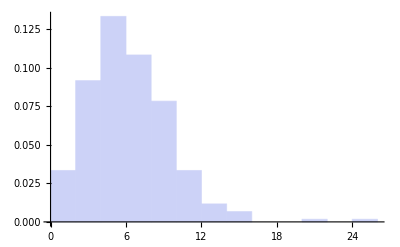
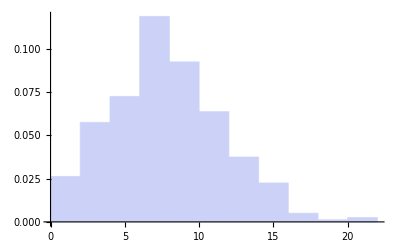
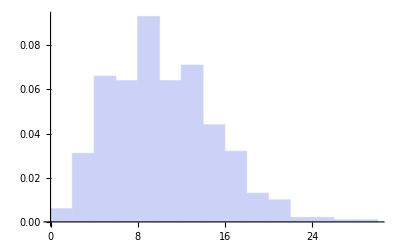
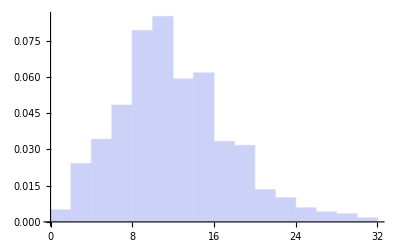
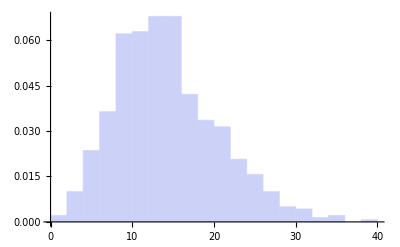
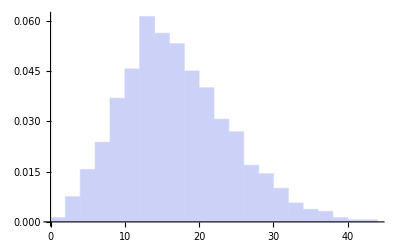

```mathematica
Table[Histogram[VertexDegree[networksM3[[i]]],Automatic,"PDF"],{i,1,10,1}]
```

{57/271,111/718,450/2881,1686/12109,3945/27233,59/408,5484/37715,1308/8695,3936/26309,15585/106003}

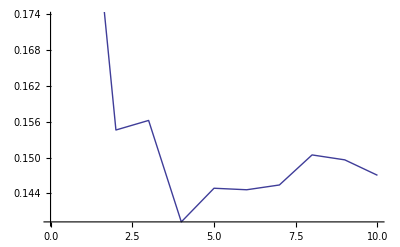

{∞,∞,∞,∞,∞,∞,∞,880321/319600,∞,675241/249750}

-Graphics-

```mathematica
clusteringM3=Map[GlobalClusteringCoefficient,networksM3]
ListPlot[clusteringM3,Joined->True]
aplM3=Map[MeanGraphDistance,networksM3]
ListPlot[aplM3,Joined->True]
```

Capacity = 2

```mathematica
ivals={100,200,300,400,500,600,700,800,900,1000};
jvals={1000,2000,3000,4000,5000,6000,7000,8000,9000,10000};
networksM3=Table[Import[StringJoin["graphs/model-v3/capacity2/","network-",IntegerString[ivals[[i]]],"-",IntegerString[jvals[[i]]],".graphml"]],{i,1,10,1}];
```

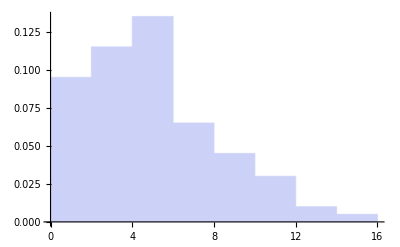
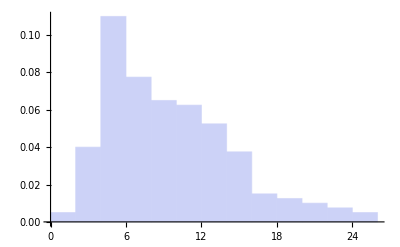
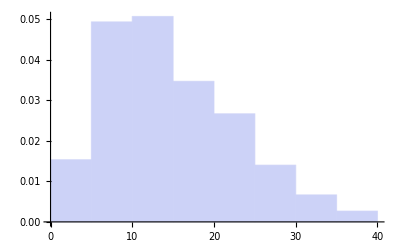
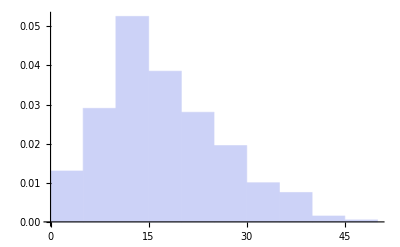
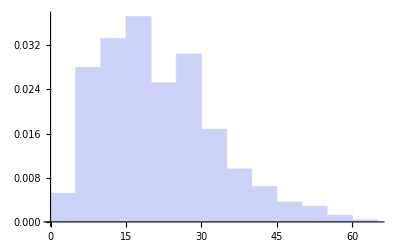
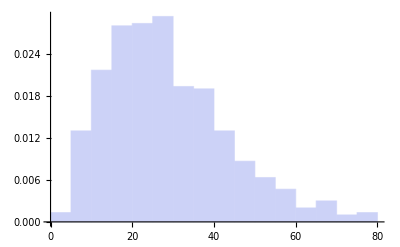
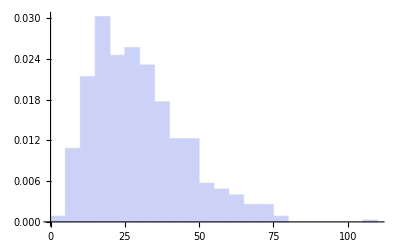
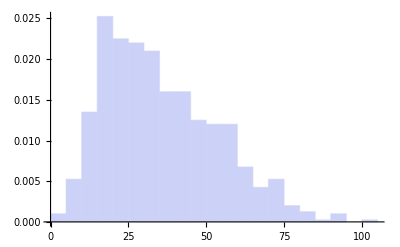

```mathematica
Table[Histogram[VertexDegree[networksM3[[i]]],Automatic,"PDF"],{i,1,10,1}]
```

{177/1355,1314/9779,5757/37663,3048/22595,6361/45594,42723/293849,52641/375091,27581/203276,39909/288043,51056/378599}

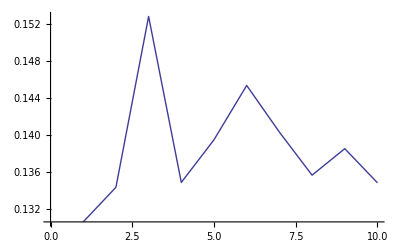

{∞,∞,∞,24748/9975,298669/124750,81593/35940,112613/48930,712677/319600,888791/404550,1088351/499500}

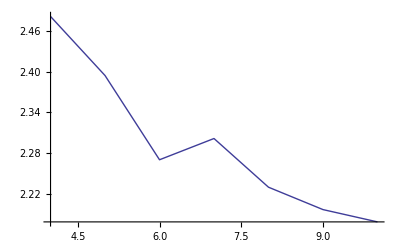

```mathematica
clusteringM3=Map[GlobalClusteringCoefficient,networksM3]
ListPlot[clusteringM3,Joined->True]
aplM3=Map[MeanGraphDistance,networksM3]
ListPlot[aplM3,Joined->True]
```

Capacity = 2

```mathematica
ivals={100,200,300,400,500,600,700,800,900,1000};
jvals={1000,2000,3000,4000,5000,6000,7000,8000,9000,10000};
networksM3=Table[Import[StringJoin["graphs/model-v3/capacity5/","network-",IntegerString[ivals[[i]]],"-",IntegerString[jvals[[i]]],".graphml"]],{i,1,10,1}];
```

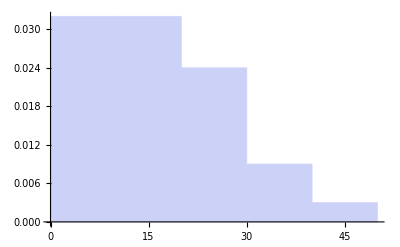
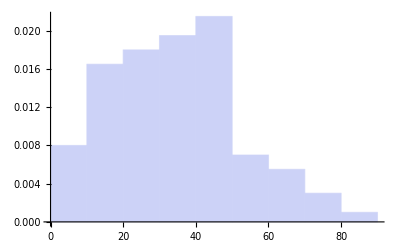
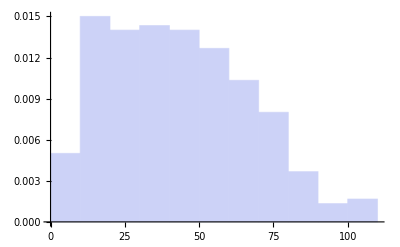
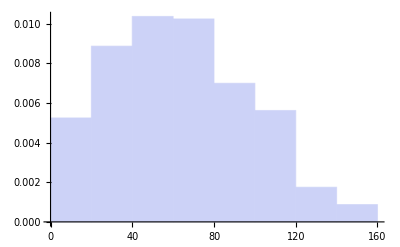
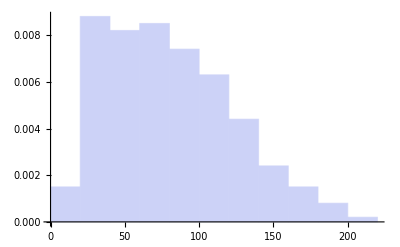
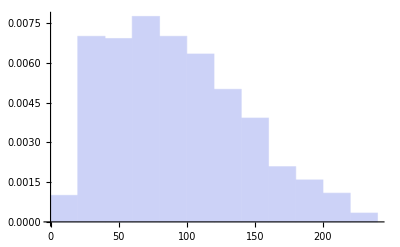
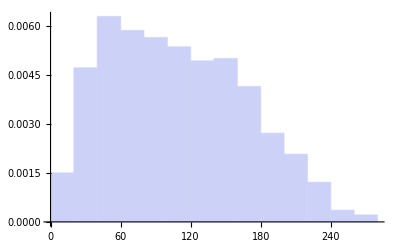
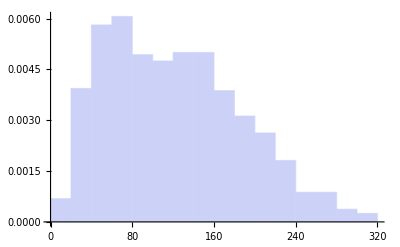

```mathematica
Table[Histogram[VertexDegree[networksM3[[i]]],Automatic,"PDF"],{i,1,10,1}]
```

{1797/5756,40368/142933,30596/118139,138822/503203,185621/670555,291414/1080581,731184/2642617,1014135/3755299,1499283/5504812,4632009/16447987}

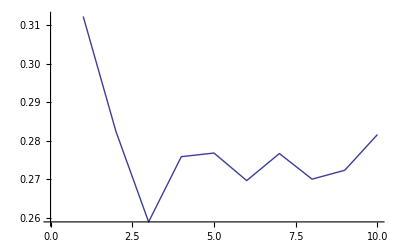

{∞,37341/19900,14288/7475,6221/3325,231061/124750,4453/2396,32429/17475,296629/159800,124928/67425,920899/499500}

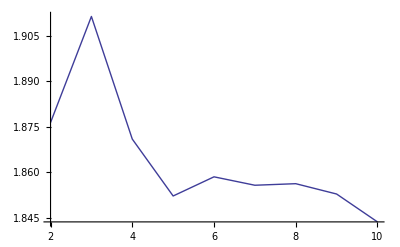

```mathematica
clusteringM3=Map[GlobalClusteringCoefficient,networksM3]
ListPlot[clusteringM3,Joined->True]
aplM3=Map[MeanGraphDistance,networksM3]
ListPlot[aplM3,Joined->True]
```